```mathematica
ClearAll["Global`*"];
ClearAll[Evaluate[Context[]<>"*"]];
SetDirectory@NotebookDirectory[]
```

/run/media/bryan/Resources/Documents/Base/4. 实验/4. 闪烁谱仪/data

```mathematica
<<"~/Documents/Base/Templates/Mathematica/MathUtils.m"
Information["Funcs`*"];
autoCollapse[];
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,siunitx}"}];

omarker=Graphics[{Thickness[.2],Disk[]}];
({colors,colorsDefault}
=colorPalette/@{"Scientific","Default"})//Grid
```

RGBColor[0.9, 0.36, 0.054] | RGBColor[0.365248, 0.427802, 0.758297] | RGBColor[0.945109, 0.593901, 0.] | RGBColor[0.645957, 0.253192, 0.685109] | RGBColor[0.285821, 0.56, 0.450773] | RGBColor[0.7, 0.336, 0.] | RGBColor[0.491486, 0.345109, 0.8] | RGBColor[0.71788, 0.568653, 0.] | RGBColor[0.70743, 0.224, 0.542415] | RGBColor[0.287228, 0.490217, 0.664674] | RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636] | RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922] | RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023] | RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854] | RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[1, 0.75, 0] | RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

```mathematica
(*SetOptions[$FrontEndSession,ShowCellLabel->False]*)
```

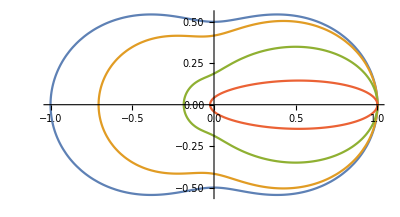

```mathematica
comptonRatio[a_,th_]:=1/(1+a(1-Cos[th]));
comptonSection[a_,th_]:=Evaluate[
Block[{p=comptonRatio[a,th]},
p^2(p+p^-1-Sin[th]^2)/2
]//Simplify
];
PolarPlot[comptonSection[#,th]&/@{0.,.1,1.,10.}//Evaluate,{th,0,2π}]
```

```mathematica
comptonElectronEnergy[a_,th_]:=Evaluate[
a(1-comptonRatio[a,th])
];
comptonThetaByEnergy[a_,e_]:=Evaluate@Module[{
th,sol,conds=0≤e≤(2 a^2)/(1+2a)&&a>0
},
sol=Assuming[conds,
Solve[comptonElectronEnergy[a,th]==e
&&Sequence@@conds
&&0≤th≤π,th,Reals
]//Refine
];
If[Dimensions[sol]≠{1,1},Abort[],th/.sol⟦1,1⟧]
];
comptonSectionByEnergy[a_,e_]:=Evaluate@Simplify[ConditionalExpression[
comptonSection[a,comptonThetaByEnergy[a,e]]
*Sin[comptonThetaByEnergy[a,e]]
*(D[comptonThetaByEnergy[a,e], e]),
0≤e≤(2 a^2)/(1+2a)
]]
comptonSectionByEnergy[α,e]//First
```

(e^2-(-2+e) e^2 α+e (-2+3 e) α^2-4 e α^3+2 α^4)/(2 α^4 (-e+α)^2)

```mathematica
comptonSpectrumAppearance[alist_]:={
Filling->Axis
,PlotLabels->Placed[
Evaluate["α = "<>ToString[#]&/@alist],
Above
]
,Epilog->Join[
(Inset[Evaluate@Style[#1
,FontFamily->"黑体"
,FontSize->10.5],#2]&)@@@{
{MaTeX["\\frac{E}{m_e c^2}"],Scaled[{1.06,0}]},
{"相对截面",Scaled[{.02,1.06}]}
},{(*ADD EPILOGS HERE*)}
]
,PlotRangeClipping->False
,ImagePadding->{{30,40},{25,30}}
};
```

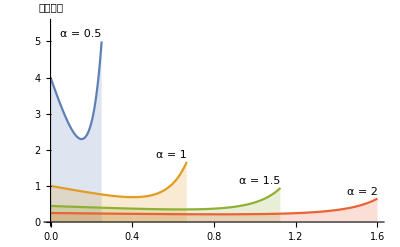

```mathematica
comptonSpectrum=Module[{alist={0.5,1,1.5,2},appearOpts},
appearOpts=comptonSpectrumAppearance[alist];
Plot[
comptonSectionByEnergy[#,e]&/@alist//Simplify//Evaluate,
{e,0,Max[alist]},
PlotRange->{0,5.5},
Evaluate[Sequence@@appearOpts]
]
];
(*exportPlot[comptonSpectrum]*)
comptonSpectrum
```

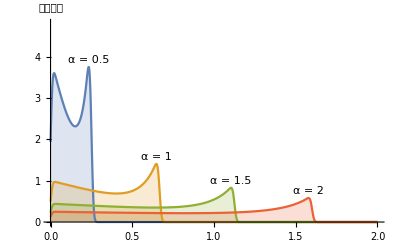

```mathematica
comptonSpectrumObs=Module[{alist={0.5,1,1.5,2},sigma=.01,appearOpts},
appearOpts=comptonSpectrumAppearance[alist];
Plot[NIntegrate[
comptonSectionByEnergy[#,e0]*PDF[
NormalDistribution[e0,sigma]
][e],
{e0,0,(2#^2)/(1+2#)}
]&/@alist//Simplify//Evaluate,
{e,0,Max[alist]},
PlotRange->{0,4.8},
Evaluate[Sequence@@appearOpts]
]//Quiet
];
(*exportPlot[comptonSpectrumObs]*)
comptonSpectrumObs
```

```mathematica
Entity["Particle","Electron"][EntityProperty["Particle","Mass"]]
```

510.9989461 keV/c^2

```mathematica
{.662,.184,1.17,1.33}/.511//Round[#,.01]&//Sort;
.662*(2#)/(1+2#)&@((.662)/(.511));
.662-.478;
hideInfo["arithmetics"]
```

### arithmetics